Quick tips before trying to solve the OLG model.
1- Determine whether the zero steady state is possible:
	
	if f(0) = 0 (or, equivalently, w(0) = 0), then the zero (autarky) steady state exists. It may be stable or unstable, but it exists.
		
		Cobb-Douglas production:

```mathematica
fCobbDouglas[k_]=k^α;
```

```mathematica
fCobbDouglas[0]=0
```

```mathematica
0
```

CES production with complementary inputs: ρ<0
		Important remark: verify the exact functional form of the production function, in particular how the exponents are written.

```mathematica
fCES[k_]=(α*k^ρ+(1-α))^(1/ρ);
		Limit[fCES[k],k-> 0,Assumptions->{ρ<0,α>0,α<1}]
```

```mathematica
0
```

If f(0) > 0, then the zero (autarky) steady states does not exist.

```mathematica
Limit[fCES[k],k-> 0,Assumptions->{ρ>0,α>0,α<1}]
```

```mathematica
(1-α)^(1/ρ)
```

2- Determine whether the interest rate appears in the savings function:
	
	if log-utility, the interest rate does not appear.

```mathematica
uprimeLogUtility[x_]=1/x;
```

```mathematica
Solve[uprimeLogUtility[w-s]==β*R*uprimeLogUtility[R*s],s]
```

```mathematica
{{s->(w β)/(1+β)}}
```

Other functional forms: CIES, R appears in the savings function:

```mathematica
uprimeCIES[x_]=x^(-1/σ);
```

```mathematica
Solve[uprimeCIES[w-s]==β*R*uprimeCIES[R*s],s]
```

```mathematica
{{s->(R^σ w β^σ)/(R+R^σ β^σ)}}
```

3 - Pick your own model!

```mathematica
f[k_,α_,ρ_]=If[ρ==0,k^α,(α*k^ρ+(1-α))^(1/ρ)];
u[x_,σ_]=If[σ==1,Log[x],x^(1-1/σ)/(1-1/σ)];
wfunction[k_,α_,ρ_]=f[k,α,ρ]-D[f[k,α,ρ],k]*k;
Rfunction[k_,α_,ρ_]=D[f[k,α,ρ],k];
```

```mathematica
savings[w_,R_,σ_,β_]:=s/.Solve[D[u[w-s,σ],s]+β*D[u[R*s,σ],s]==0,s][[1]]
```

```mathematica
derivative[k1_,k_,α_,β_,σ_,ρ_,n_]:=-D[k1-1/(1+n)*(savings[w,R,σ,β]/.{w-> wfunction[k,α,ρ],R-> Rfunction[k1,α,ρ]}),k]/D[k1-1/(1+n)*(savings[w,R,σ,β]/.{w-> wfunction[k,α,ρ],R-> Rfunction[k1,α,ρ]}),k1]
```

```mathematica
der[sols_,i_,α_,β_,σ_,ρ_,n_]:=Limit[derivative[k1,k0,α,β,σ,ρ,n],{k0,k1}-> {k/.sols[[i]],k1-> k/.sols[[i]]},Direction->{"FromAbove","FromAbove"}]
```

```mathematica
stability[α_,β_,σ_,ρ_,n_]:=(If[Length[NSolve[k==1/(1+n)*savings[w,R,σ,β]/.{w-> wfunction[k,α,ρ],R-> Rfunction[k,α,ρ]},k,Reals]]==0,sols={{k-> 0}},sols=NSolve[k==1/(1+n)*savings[w,R,σ,β]/.{w-> wfunction[k,α,ρ],R-> Rfunction[k,α,ρ]},k,Reals]];For[i=1,i≤ Length[sols],Print["                  Steady state ",i,", Capital level: ",k/.sols[[i]],": Derivative=",der[sols,i, α,β,σ,ρ,n],If[-1<der[sols,i, α,β,σ,ρ,n]<1," Stable"," Unstable"]];i++])
```

```mathematica
myprogram[α_,β_,σ_,ρ_,n_]:=(Print[
"Production function:    f(k)=",f[k,α,ρ], "\n",
"Utility function:       u(c)=",u[c,σ],"\n",
"Savings function:       s(w(",Subscript[k,t],"),",Subsuperscript["k","t+1","'"],"))= ",savings[w,R,σ,β],"\n",
"Substituting:           s(w(",Subscript[k,t],"),",Subsuperscript["k","t+1","'"],"))= ",savings[w,R,σ,β]/.{w-> wfunction[k,α,ρ],R-> Rfunction[k,α,ρ]},"\n",
"Steady States:          Solve ", Subscript["k","t+1"]," == 1/(1+n)s(w(",Subscript[k,t],"),",Subsuperscript["k","t+1","'"],"))","\n",
"   With the parameters: ",Quiet[If[Length[NSolve[k==1/(1+n)*savings[w,R,σ,β]/.{w-> wfunction[k,α,ρ],R-> Rfunction[k,α,ρ]},k,Reals]]==0,{{k-> 0}},NSolve[k==1/(1+n)*savings[w,R,σ,β]/.{w-> wfunction[k,α,ρ],R-> Rfunction[k,α,ρ]},k,Reals]]],"\n",
"Stability:             Compute the derivative of ",Subscript["k","t+1"]," with respect to ",Subscript["k","t"]," and evaluate at each steady state","\n",
"   With the parameters: "];Print[Quiet[stability[α,β,σ,ρ,n]]];solsSimple=k/.sols;If[Max[solsSimple]==0,maxk=0.5,maxk=1.2*Max[solsSimple]];
Quiet[ContourPlot[{k1==k,k1==1/(1+n)*(savings[w,R,σ,β]/.{w-> wfunction[k,α,ρ],R-> Rfunction[k1,α,ρ]})},{k,0,maxk},{k1,0,maxk}]])
```

Production function:    f(k)=k^0.5
Utility function:       u(c)=2 √c
Savings function:       s(w(k_t),k'_(t+1)))= (16. R w)/(25.+16. R)
Substituting:           s(w(k_t),k'_(t+1)))= 4./(25.+8./k^0.5)
Steady States:          Solve k_(t+1) == 1/(1+n)s(w(k_t),k'_(t+1)))
   With the parameters: {{k→0.},{k→0.0733398}}
Stability:             Compute the derivative of k_(t+1) with respect to k_t and evaluate at each steady state
   With the parameters:

Steady state 1, Capital level: 0.: Derivative=∞ Unstable

Steady state 2, Capital level: 0.0733398: Derivative=0.406773 Stable

Null

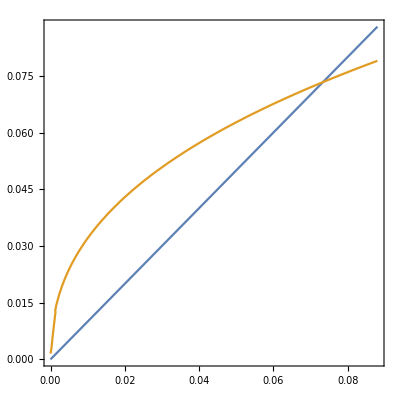

```mathematica
myprogram[0.5,0.8,2,0,0]
```

Production function:    f(k)=1/(√(0.5+0.5/k^2))
Utility function:       u(c)=2 √c
Savings function:       s(w(k_t),k'_(t+1)))= (16. R w)/(25.+16. R)
Substituting:           s(w(k_t),k'_(t+1)))= (8. (1/(√(0.5+0.5/k^2))-0.5/((0.5+0.5/k^2)^(3/2) k^2)))/((25.+8./((0.5+0.5/k^2)^(3/2) k^3)) (0.5+0.5/k^2)^(3/2) k^3)
Steady States:          Solve k_(t+1) == 1/(1+n)s(w(k_t),k'_(t+1)))
   With the parameters: {{k→0}}
Stability:             Compute the derivative of k_(t+1) with respect to k_t and evaluate at each steady state
   With the parameters:

Steady state 1, Capital level: 0: Derivative=0. Stable

Null

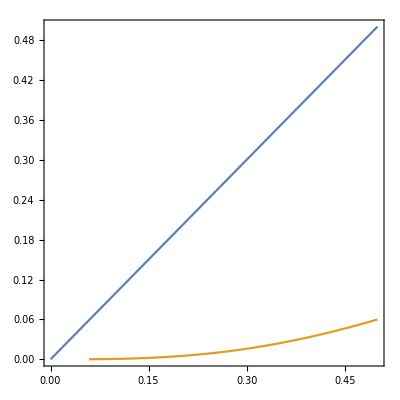

```mathematica
myprogram[0.5,0.8,2,-2,0]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Production function:    f(k)=1/(√(0.5+0.5/k^2))
Utility function:       u(c)=Log[c]
Savings function:       s(w(k_t),k'_(t+1)))= 0.444444 w
Substituting:           s(w(k_t),k'_(t+1)))= 0.444444 (1/(√(0.5+0.5/k^2))-0.5/((0.5+0.5/k^2)^(3/2) k^2))
Steady States:          Solve k_(t+1) == 1/(1+n)s(w(k_t),k'_(t+1)))
   With the parameters: {{k→0}}
Stability:             Compute the derivative of k_(t+1) with respect to k_t and evaluate at each steady state
   With the parameters:

Steady state 1, Capital level: 0: Derivative=0. Stable

Null

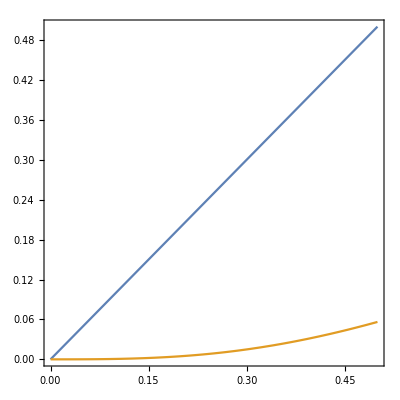

```mathematica
myprogram[0.5,0.8,1,-2,0]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Production function:    f(k)=(0.5+0.5 k^0.5)^2.
Utility function:       u(c)=Log[c]
Savings function:       s(w(k_t),k'_(t+1)))= 0.444444 w
Substituting:           s(w(k_t),k'_(t+1)))= 0.444444 ((0.5+0.5 k^0.5)^2.-0.5 (0.5+0.5 k^0.5)^1. k^0.5)
Steady States:          Solve k_(t+1) == 1/(1+n)s(w(k_t),k'_(t+1)))
   With the parameters: {{k→0.154832}}
Stability:             Compute the derivative of k_(t+1) with respect to k_t and evaluate at each steady state
   With the parameters:

Steady state 1, Capital level: 0.154832: Derivative=0.141188 Stable

Null

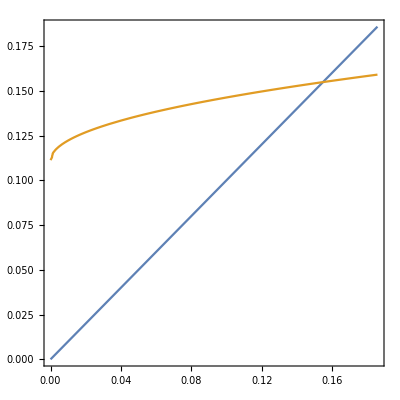

```mathematica
myprogram[0.5,0.8,1,0.5,0]
```

Production function:    f(k)=(0.5+0.5 k^0.5)^2.
Utility function:       u(c)=2 √c
Savings function:       s(w(k_t),k'_(t+1)))= (16. R w)/(25.+16. R)
Substituting:           s(w(k_t),k'_(t+1)))= (8. (0.5+0.5 k^0.5)^1. ((0.5+0.5 k^0.5)^2.-0.5 (0.5+0.5 k^0.5)^1. k^0.5))/((25.+(8. (0.5+0.5 k^0.5)^1.)/k^0.5) k^0.5)
Steady States:          Solve k_(t+1) == 1/(1+n)s(w(k_t),k'_(t+1)))
   With the parameters: {{k→0.128222}}
Stability:             Compute the derivative of k_(t+1) with respect to k_t and evaluate at each steady state
   With the parameters:

Steady state 1, Capital level: 0.128222: Derivative=0.107258 Stable

Null

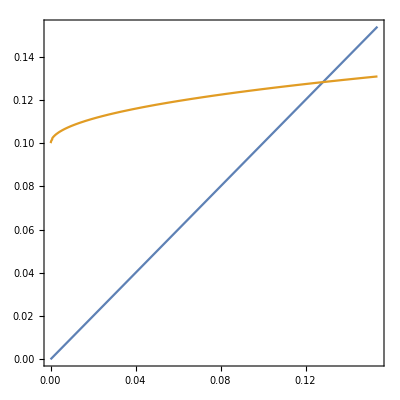

```mathematica
myprogram[0.5,0.8,2,0.5,0]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Production function:    f(k)=k^0.5
Utility function:       u(c)=Log[c]
Savings function:       s(w(k_t),k'_(t+1)))= 0.444444 w
Substituting:           s(w(k_t),k'_(t+1)))= 0.222222 k^0.5
Steady States:          Solve k_(t+1) == 1/(1+n)s(w(k_t),k'_(t+1)))
   With the parameters: {{k→0.},{k→0.0493827}}
Stability:             Compute the derivative of k_(t+1) with respect to k_t and evaluate at each steady state
   With the parameters:

Steady state 1, Capital level: 0.: Derivative=∞ Unstable

Steady state 2, Capital level: 0.0493827: Derivative=0.5 Stable

Null

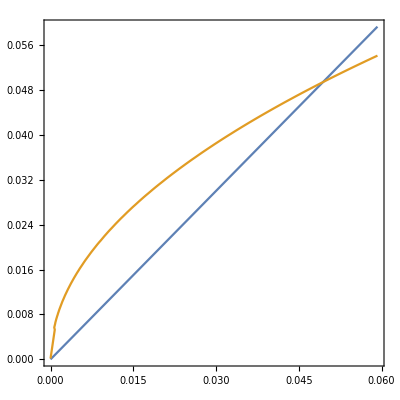

```mathematica
myprogram[0.5,0.8,1,0,0]
```

```mathematica
myprogram[0.1,0.8,2,-1,0]
```

Production function:    f(k)=1/(0.9+0.1/k)
Utility function:       u(c)=2 √c
Savings function:       s(w(k_t),k'_(t+1)))= (16. R w)/(25.+16. R)
Substituting:           s(w(k_t),k'_(t+1)))= (1.6 (1/(0.9+0.1/k)-0.1/((0.9+0.1/k)^2 k)))/((25.+1.6/((0.9+0.1/k)^2 k^2)) (0.9+0.1/k)^2 k^2)
Steady States:          Solve k_(t+1) == 1/(1+n)s(w(k_t),k'_(t+1)))
   With the parameters: {{k→0.018251},{k→0.206304}}
Stability:             Compute the derivative of k_(t+1) with respect to k_t and evaluate at each steady state
   With the parameters:

$Aborted

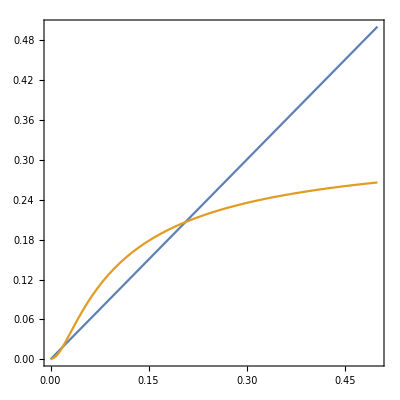

```mathematica
ContourPlot[{k1==k,k1==1/(1+0)*(savings[w,R,2,0.8]/.{w-> wfunction[k,0.1,-1],R-> Rfunction[k1,0.1,-1]})},{k,0,maxk},{k1,0,maxk}]
```

```mathematica
Export["xamples.pdf",EvaluationNotebook[]]
```

xamples.pdf